```mathematica
TeXForm[D[ρ[r]*u[r]^3 /2+ γ*u[r]*p[r]/(γ-1),r] + ρ[r]*u[r]^3/(2*r) +γ*u[r] p[r]/(γ-1)/r ]
```

\frac{\gamma  u(r) p'(r)}{\gamma -1}+\frac{\gamma  p(r) u'(r)}{\gamma -1}+\frac{\gamma  p(r)
   u(r)}{(\gamma -1) r}+\frac{3}{2} \rho (r) u(r)^2 u'(r)+\frac{1}{2} u(r)^3 \rho
   '(r)+\frac{\rho (r) u(r)^3}{2 r}

```mathematica
D[ρ[r]*u[r],r] + ρ[r]*u[r]/r
D[ρ[r]*u[r]^2 + p[r],r] + ρ[r]*u[r]^2/r 
D[ρ[r]*u[r]^3 /2+ γ*u[r]*p[r]/(γ-1),r] + ρ[r]*u[r]^3/(2*r) +γ*u[r] p[r]/(γ-1)/r
```

(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]

(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]

(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]

```mathematica
Решаем
```

```mathematica
γ=2.0;
r1=0.3;
F=1;
s=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]*u[r]/ρ[r],u[0.1]==1,ρ[0.1]==1,p[0.1]==0.05},{ρ,u,p},{r,0.1,r1}]
```

{{ρ→InterpolatingFunction[{{0.1, 0.3}}, <>],u→InterpolatingFunction[{{0.1, 0.3}}, <>],p→InterpolatingFunction[{{0.1, 0.3}}, <>]}}

```mathematica
""
```

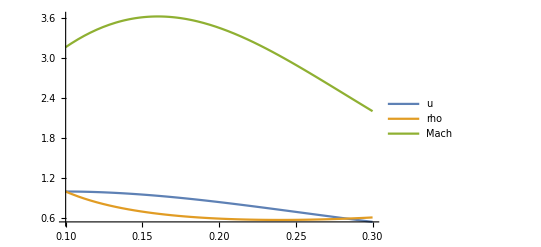

```mathematica
Plot[{Evaluate[u[r]/. s], Evaluate[ρ[r]/. s], Evaluate[u[r]/Sqrt[(γ * p[r]/ρ[r])]/. s]},{r,0.1,r1},PlotRange->All,PlotLegends->{"u","rho","Mach"}]
```

```mathematica
DD = 0;
ro1 =ρ[r1]/. s
p1 = p[r1]/. s
u1 = u[r1]/. s
F=1;
g = 2.0;
ss = NSolve[ro1*(u1-DD)==ro*(u-DD)&&ro1*u1*(u1 - DD) + p1 == ro*u*(u - DD)+ p&& ro1*(u1 - DD)*(p1/(ro1*(g-1)) + u1^2/2) + p1 * u1==ro*(u - DD)*(p/(ro*(g-1)) + (u^2)/2) + p * u ,{ro, u, p},Reals]
```

{0.611674}

{0.0187072}

{0.544953}

{{p→0.114865,ro→1.29965,u→0.25648},{p→0.0187072,ro→0.611674,u→0.544953}}

```mathematica
g1=u/. ss[[1]];
g2=ro/. ss[[1]];
g3=p/. ss[[1]];
r2=1.4;
sss=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]u[r]/ρ[r],u[r1]==g1,ρ[r1]==g2,p[r1]==g3},{ρ,u,p},{r,r1,r2}]
```

{{ρ→InterpolatingFunction[{{0.3, 1.4}}, <>],u→InterpolatingFunction[{{0.3, 1.4}}, <>],p→InterpolatingFunction[{{0.3, 1.4}}, <>]}}

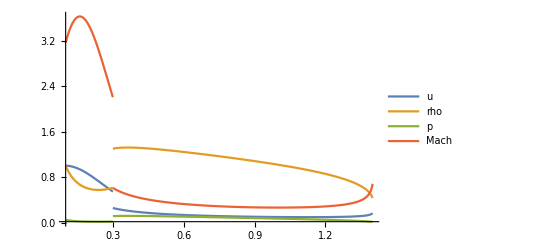

```mathematica
Show[Plot[{Evaluate[u[r]/. s], Evaluate[ρ[r]/. s], Evaluate[p[r]/. s],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. s]},{r,0.1,r1},PlotRange->All,PlotLegends->{"u","rho","p","Mach"}],Plot[{Evaluate[u[r]/. sss],Evaluate[ρ[r]/. sss], Evaluate[p[r]/. sss],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. sss]},{r,r1,r2},PlotRange->All]]
```

```mathematica
u[r2]/. sss
ρ[r2]/. sss
p[r2]/. sss
```

{0.0948223}

{0.753288}

{0.224293}

```mathematica
g1=u[r2]/. sss;
g2=ρ[r2]/. sss;
g3=p[r2]/. sss;
r3=0.583;
ssss=NDSolve[{(u[r] ρ[r])/r+ρ[r] u'[r]+u[r] ρ'[r]==0,(u[r]^2 ρ[r])/r+p'[r]+2 u[r] ρ[r] u'[r]+u[r]^2 ρ'[r]==-F*u[r]/ρ[r],(γ p[r] u[r])/(r (-1+γ))+(u[r]^3 ρ[r])/(2 r)+(γ u[r] p'[r])/(-1+γ)+(γ p[r] u'[r])/(-1+γ)+3/2 u[r]^2 ρ[r] u'[r]+1/2 u[r]^3 ρ'[r]==-F*u[r]*u[r]/ρ[r],u[r2]==g1,ρ[r2]==g2,p[r2]==g3},{ρ,u,p},{r,r2,r3}]
```

{{ρ→InterpolatingFunction[…],u→InterpolatingFunction[…],p→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.300006} lies outside the range of data in the interpolating function. Extrapolation will be used.

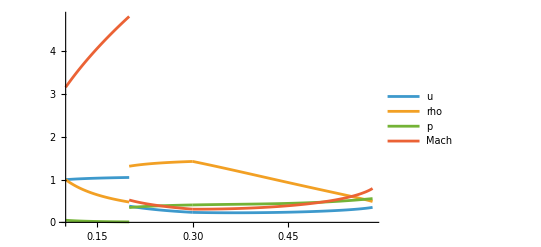

```mathematica
Show[Plot[{Evaluate[u[r]/. s], Evaluate[ρ[r]/. s], Evaluate[p[r]/. s],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. s]},{r,0.1,r1},PlotRange->All,PlotLegends->{"u","rho","p","Mach"}],Plot[{Evaluate[u[r]/. sss],Evaluate[ρ[r]/. sss], Evaluate[p[r]/. sss],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. sss]},{r,r1,r2},PlotRange->All],Plot[{Evaluate[u[r]/. ssss],Evaluate[ρ[r]/. ssss], Evaluate[p[r]/. sss],Evaluate[u[r]/Sqrt[(g * p[r]/ρ[r])]/. ssss]},{r,r2,r3},PlotRange->All]]
```

```mathematica
xValues=Range[0.17,0.8,0.15]; (*шаг 0.1*)
pValues=u[xValues]/. sss;
Export["D:sss.csv",pValues,"CSV"];
xValues
pValues
```

{0.17,0.32,0.47,0.62,0.77}

{{0.310108,0.16538,0.121538,0.101124,0.0916454}}

```mathematica
T = {{0.17,0.31010790623201573},{0.32,0.16537987485834005},{0.47,0.12153843156423706},{0.7700000000000001,0.09164542330087837}};
poly=InterpolatingPolynomial[T,r]
```

0.0916454+(-0.364104+(0.881536-3.02309 (-0.47+r)) (-0.17+r)) (-0.77+r)

```mathematica
0.1373819908048013+(-0.1812890357271155+(-0.5476813166387459+1.3895503902487591 (-0.37+r)) (-0.17+r)) (-0.7700000000000001+r)
```

```mathematica
Линейная теория
```

```mathematica
Collect[D[(ρ1[r] + ϵ*ρ2[r])*(u1[r] + ϵ*u2[r]),r] +(ρ1[r] + ϵ*ρ2[r])*(u1[r] + ϵ*u2[r])/r,ϵ]
```

(u1[r] ρ1[r])/r+ρ1[r] u1'[r]+u1[r] ρ1'[r]+ϵ ((u2[r] ρ1[r])/r+(u1[r] ρ2[r])/r+ρ2[r] u1'[r]+ρ1[r] u2'[r]+u2[r] ρ1'[r]+u1[r] ρ2'[r])+ϵ^2 ((u2[r] ρ2[r])/r+ρ2[r] u2'[r]+u2[r] ρ2'[r])

```mathematica
(u1[r] + ϵ*u2[r])
(ρ1[r] + ϵ*ρ2[r])
(p1[r] + ϵ*p2[r])
```

```mathematica
TeXForm[((u2[r] ρ1[r])/r+(u1[r] ρ2[r])/r+ρ2[r] u1'[r]+ρ1[r] u2'[r]+u2[r] ρ1'[r]+u1[r] ρ2'[r])]
```

\text{$\rho $2}(r) \text{u1}'(r)+\text{u1}(r) \text{$\rho $2}'(r)+\frac{\text{$\rho $2}(r)
   \text{u1}(r)}{r}+\text{$\rho $1}(r) \text{u2}'(r)+\text{u2}(r) \text{$\rho
   $1}'(r)+\frac{\text{$\rho $1}(r) \text{u2}(r)}{r}

```mathematica
Collect[D[(ρ1[r] + ϵ*ρ2[r])*(u1[r] + ϵ*u2[r])^2 + (p1[r] + ϵ*p2[r]),r] + (ρ1[r] + ϵ*ρ2[r])*(u1[r] + ϵ*u2[r])^2/r ,ϵ]
```

(u1[r]^2 ρ1[r])/r+p1'[r]+2 u1[r] ρ1[r] u1'[r]+u1[r]^2 ρ1'[r]+ϵ ((2 u1[r] u2[r] ρ1[r])/r+(u1[r]^2 ρ2[r])/r+p2'[r]+2 u2[r] ρ1[r] u1'[r]+2 u1[r] ρ2[r] u1'[r]+2 u1[r] ρ1[r] u2'[r]+2 u1[r] u2[r] ρ1'[r]+u1[r]^2 ρ2'[r])+ϵ^2 ((u2[r]^2 ρ1[r])/r+(2 u1[r] u2[r] ρ2[r])/r+2 u2[r] ρ2[r] u1'[r]+2 u2[r] ρ1[r] u2'[r]+2 u1[r] ρ2[r] u2'[r]+u2[r]^2 ρ1'[r]+2 u1[r] u2[r] ρ2'[r])+ϵ^3 ((u2[r]^2 ρ2[r])/r+2 u2[r] ρ2[r] u2'[r]+u2[r]^2 ρ2'[r])

```mathematica
TeXForm[((2 u1[r] u2[r] ρ1[r])/r+(u1[r]^2 ρ2[r])/r+p2'[r]+2 u2[r] ρ1[r] u1'[r]+2 u1[r] ρ2[r] u1'[r]+2 u1[r] ρ1[r] u2'[r]+2 u1[r] u2[r] ρ1'[r]+u1[r]^2 ρ2'[r])]
```

\text{p2}'(r)+2 \text{$\rho $2}(r) \text{u1}(r) \text{u1}'(r)+2 \text{$\rho $1}(r) \text{u2}(r)
   \text{u1}'(r)+\text{u1}(r)^2 \text{$\rho $2}'(r)+\frac{\text{$\rho $2}(r)
   \text{u1}(r)^2}{r}+2 \text{$\rho $1}(r) \text{u1}(r) \text{u2}'(r)+2 \text{u1}(r)
   \text{u2}(r) \text{$\rho $1}'(r)+\frac{2 \text{$\rho $1}(r) \text{u1}(r) \text{u2}(r)}{r}

```mathematica
((2 u1[r] u2[r] ρ1[r])/r+(u1[r]^2 ρ2[r])/r+p2'[r]+2 u2[r] ρ1[r] u1'[r]+2 u1[r] ρ2[r] u1'[r]+2 u1[r] ρ1[r] u2'[r]+2 u1[r] u2[r] ρ1'[r]+u1[r]^2 ρ2'[r])//FullSimplify
```

(r (p2'[r]+2 u2[r] ρ1[r] u1'[r])+2 u1[r] (r ρ2[r] u1'[r]+r ρ1[r] u2'[r]+u2[r] (ρ1[r]+r ρ1'[r]))+u1[r]^2 (ρ2[r]+r ρ2'[r]))/r